Biological Modelling and Model Analysis - day VII

Unravelling complex dynamics by a separation of time-scales

Franjo Weissing & Sander van Doorn

Groningen Institute for Evolutionary Life Sciences

g.s.van.doorn@rug.nl

## Bursting in pancreatic β-cells

### Model definition

Pancreatic β-cells play a key role in the regulation of the blood glucose concentration. Their primary function is to produce, store and release the hormone insulin. β-cells in an intact islet of Langerhans exhibit bursting electrical activity, i.e., they alternate between periods of spontaneous electrical spiking and a resting state without rapid electrical activity. This behaviour is thought to be regulated by the intracellular Ca^(2+)concentration. The electrical activity of β-cells can be described by the following model, which was originally suggested by Catherine Morris and Harold Lecar (Biophys. J. 35: 193-213 (1981)):

```mathematica
eqV[V_,W_,Ca_]:=(J-Subscript[g, ca] Subscript[m, ∞][V](V-Subscript[v, ca])-(Subscript[g, k] W+Subscript[g, kca] z[Ca] )(V-Subscript[v, K])-Subscript[g, l](V-Subscript[v, l]))/Cm
eqW[V_,W_]:=0.23  (Subscript[w, ∞][V]-W)/τ[V]
```

```mathematica
Subscript[m, ∞][V_]:=1/2(1+Tanh[(V+1.2)/18.])
Subscript[w, ∞][V_]:=1/2(1+Tanh[(V-12.)/17.4])
z[Ca_]:=Ca/(10.+Ca)
τ[V_]:=1/Cosh[(V-12.)/34.8]
```

```mathematica
pars={Subscript[g, ca]->4., Subscript[v, ca]->120.,Subscript[g, k]->8.,Subscript[g, kca] -> .25,Subscript[v, K]->-84.,Subscript[g, l]-> 2.,Subscript[v, l]->-60.,J->45.,Cm->20.0}
```

{g_ca→4.,v_ca→120.,g_k→8.,g_kca→0.25,v_K→-84.,g_l→2.,v_l→-60.,J→45.,Cm→20.}

You will perhaps recognise that the structure of the model is similar to the Hodgkin-Huxley model. The first equation describes the change of the membrane potential (V) as a consequence of four currents: an external stimulus current J, a voltage-dependent Ca^(2+)current, a voltage-dependent K^+current, and a leak current. The conductivity of the membrane for K^+ is captured by the gating variable W, which changes on a fast time scale according to the second equation. Some of the K^+channels are sensitive to the intracellular Ca^(2+)concentration, so the model includes a calcium-dependent contribution g_kca z[Ca] to the K^+conductivity. The parameters g_ca, g_k, g_kca and g_l correspond to the maximum conductances for each respective current component and v_ca, v_k, v_l are the equilibrium membrane potentials for the calcium, potassium and leak currents in isolation. C_m is the membrane capacitance. The functions m_∞,  w_∞ and τ were fitted to data from patch-clamp and biochemical experiments.

### Equilibria and their stability

The model has complicated non-linear terms, so it is not possible to obtain explicit solution for the equilibria. However, we can solve for the equilibrium value of W...

```mathematica
solW=Solve[eqW[V,W]==0,W]//First
```

{W→0.5 (1.+Tanh[0.0574713 (-12.+V)])}

... and use this result to plot the equilibrium values of V as a function of the intracellular  Ca^(2+)concentration.

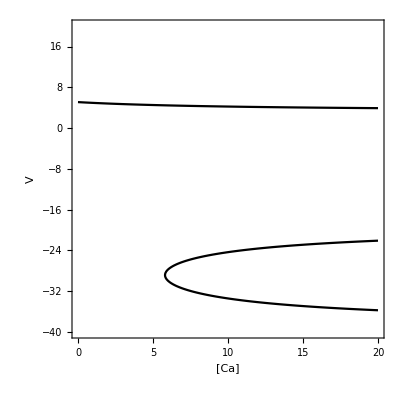

```mathematica
equilibria=ContourPlot[0==(eqV[V,W,Ca]/.solW/.pars),{Ca,0,20},{V,-40,20},PlotPoints->100,ContourStyle->Black,FrameLabel->{"[Ca]","V"}]
```

As you can see, there is a single equilibrium for low Ca^(2+)concentrations. Two additional equilibria appear at high Ca^(2+)concentrations.

Use the following procedure to determine the stability of the equilibria:

```mathematica
stabilityAnalysis[Ca_]:=Module[{eql,eqi,J},
Off[NSolve::ratnz];eql=NSolve[{eqV[V,W,Ca]==0.0,eqW[V,W]==0.0}/.pars,{V,W},Reals];
Print["Number of equilibria: ", Length[eql]];

(* stability analysis *)
J = D[{eqV[V,W,Ca],eqW[V,W]}/.pars,{{V,W}}];
Do[
eqi=eql[[i]] ;
Print["equilibrium ", i, ": ", eqi];
Print["   eigenvalues: ",J/.eqi//Eigenvalues];
,{i,1, Length[eql]}]
]
```

```mathematica
stabilityAnalysis[15.0]
```

Number of equilibria: 3

equilibrium 1: {V→-34.9356,W→0.00451919}

eigenvalues: {-0.461599,-0.0477878}

equilibrium 2: {V→-22.9012,W→0.0177818}

eigenvalues: {-0.314467,0.0675857}

equilibrium 3: {V→4.02935,W→0.28574}

eigenvalues: {0.00335306+0.371044 ⅈ,0.00335306-0.371044 ⅈ}

Q3: Determine the stability and type (node, saddle or spiral) of the three equilibria that occur at Ca=15.

Q4: Use the procedure stabilityAnalysis[] to investigate the sudden appearance of the lower two equilibria between Ca=5.801 and Ca=5.802. Which bifurcation occurs here?

Q5: Now focus on the upper equilibrium and verify that it undergoes a Hopf bifurcation. Locate the exact position of the bifurcation point.

At a Hopf bifurcation, the stability of the equilibrium will change, meaning the real part of the eigenvalues changes signs. Find this point for the upper equilibrium (equilibrium 3)

Q6: Copy the above plot of the equilibrium values on a piece of paper, but use different line styles to distinguish between stable and unstable equilibria (e.g., use a dashed line for the unstable equilibria). Also indicate the position of the bifurcation points.

### A stable periodic solution

Hopf bifurcations give rise to limit cycles, which can be either stable or unstable. To find out which cycles appear in the model, we solve the model numerically and show the trajectories in a phaseportrait with null-clines and vector field.

```mathematica
phasePortrait[Ca_,initialConditions_List:{}]:=Module[{eql,fixedPoints,nullClines,vectorField,sys,vars,tEnd,init,solution,trajectories},
(* locate equilibria *)
Off[NSolve::ratnz];eql=NSolve[{eqV[V,W,Ca]==0.0,eqW[V,W]==0.0}/.pars,{V,W},Reals];
fixedPoints = ListPlot[{V, W} /. eql , PlotStyle -> {{Black, PointSize[0.02]}},PlotRange -> {{-40, 20}, {-0.1, 0.6}},Frame->True,FrameLabel->{"V","W"},AspectRatio->1];

(* draw null clines *)
nullClines = ContourPlot[{(eqV[V, W,Ca] /. pars) == 0, (eqW[V, W] /. pars) == 0}, {V, -40, 20}, {W, -0.1, 0.6},Frame->True,FrameLabel->{"V","W"},AspectRatio->1,PlotPoints -> 100, ContourStyle ->{{Dashed,Orange},{Dashed, Darker[Red]}}];

(* draw vector field *)
vectorField = VectorPlot[{eqV[V, W,Ca], eqW[V, W]}/.pars, {V, -40, 20}, {W, -0.1, 0.6},VectorStyle-> Gray,VectorPoints->Fine,PlotRange -> {{-40, 20}, {-0.1, 0.6}},Frame->True,FrameLabel->{"V","W"},AspectRatio->1];

(* run simulations *)
If[Length[initialConditions]>0,
sys ={D[V[t], t] == eqV[V[t], W[t], Ca], D[W[t], t] == eqW[V[t], W[t]]} /. pars;
vars = {V[t], W[t]};
tEnd=1000.0;
trajectories=Reap[Do[
init=Thread[{V[0],W[0]}==initialConditions[[i]]] ;
solution = NDSolve[Join[sys, init], vars, {t, 0, tEnd}];
Print["Trajectory ", i," : initial point ", init , ", final point ", Thread[{V[tEnd],W[tEnd]}=={V[t],W[t]}]/.solution/.{t->tEnd}];
Sow[ParametricPlot[vars /. solution, {t, 0, tEnd},PlotRange->All,PlotStyle->Darker[Blue]]]
,{i,1,Length[initialConditions]}]][[2,1]];Show[vectorField,trajectories,nullClines,fixedPoints],
Show[vectorField,nullClines,fixedPoints]]
]
```

Here is a phaseportrait at Ca=9.3, slightly above the Hopf bifurcation point, where the upper equilibrium is unstable

Trajectory 1 : initial point {V[0]==8,W[0]==0.43}, final point {{V[1000.]==-33.1138,W[1000.]==0.00556599}}

Trajectory 2 : initial point {V[0]==8,W[0]==0.42}, final point {{V[1000.]==-12.5442,W[1000.]==0.0421124}}

Trajectory 3 : initial point {V[0]==-0.24,W[0]==0.28}, final point {{V[1000.]==-11.0695,W[1000.]==0.196296}}

Trajectory 4 : initial point {V[0]==-30.,W[0]==-0.1}, final point {{V[1000.]==10.8044,W[1000.]==0.170189}}

Trajectory 5 : initial point {V[0]==-31.,W[0]==-0.1}, final point {{V[1000.]==-33.1138,W[1000.]==0.00556599}}

Trajectory 1 : initial point {V[0]==-17.6538,W[0]==0.0364878}, final point {{V[1000.]==9.39586,W[1000.]==0.153969}}

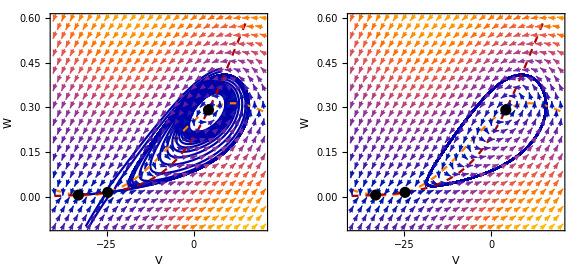

```mathematica
GraphicsRow[{phasePortrait[9.3,{{8,0.43},{8,0.42},{-0.24,0.28},{-30.0,-0.1},{-31.0,-0.1}}],
phasePortrait[9.3,{{-17.653803731772097,0.03648783622081585}}]},ImageSize->Large]
```

As expected, there is a limit cycle (for clarity, the cycle is shown by itself in the panel on the right). The cycle is easy to spot since it is stable; it attracts three of the trajectories. The other two converge on the lower equilibrium, which is stable as well.

Q7: What is the relationship between the two alternative attractors (the two stable equilibria) of the model and the different types of behaviours exhibited by a bursting pancreatic β-cell?

Is the observed cycle the one that emerges from the Hopf bifurcation point? To find out, we also construct a phaseportrait at Ca=9.2, slightly below the Hopf bifurcation point, where the upper equilibrium is stable:

Trajectory 1 : initial point {V[0]==8,W[0]==0.43}, final point {{V[1000.]==-33.0632,W[1000.]==0.0055983}}

Trajectory 2 : initial point {V[0]==8,W[0]==0.42}, final point {{V[1000.]==14.1643,W[1000.]==0.226162}}

Trajectory 3 : initial point {V[0]==-0.24,W[0]==0.28}, final point {{V[1000.]==-18.34,W[1000.]==0.0448697}}

Trajectory 4 : initial point {V[0]==-30.,W[0]==-0.1}, final point {{V[1000.]==4.43863,W[1000.]==0.39403}}

Trajectory 5 : initial point {V[0]==-31.,W[0]==-0.1}, final point {{V[1000.]==-33.0632,W[1000.]==0.0055983}}

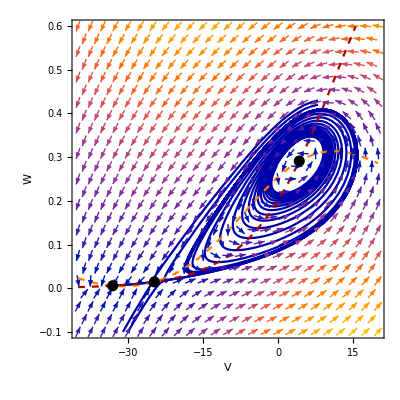

```mathematica
phasePortrait[9.2,{{8,0.43},{8,0.42},{-0.24,0.28},{-30.0,-0.1},{-31.0,-0.1}}]
```

As you can see, the phase-portrait has changed very little. In particular, the stable limit cycle is still there, ruling out the hypothesis that it emerged from the Hopf bifurcation. Weirdly enough, there is now a stable equilibrium point inside a stable limit cycle!

Q8: Verify that the upper equilibrium really is stable at at Ca=9.2 and attempt to reconcile this fact with the observation that the equilibrium is enclosed by a stable limit cycle.

The stability of the equilibrium point can be verified by performing a linear stability analysis. Indeed, for the upper equilibrium, the eigenvalues of the Jacobian have negative real parts, proving that the equilibrium is stable with respect to small, local perturbations

```mathematica
stabilityAnalysis[9.2]
```

Number of equilibria: 3

equilibrium 1: {V→-33.0632,W→0.0055983}

eigenvalues: {-0.437204,-0.0348252}

equilibrium 2: {V→-24.7233,W→0.0144705}

eigenvalues: {-0.335692,0.0444141}

equilibrium 3: {V→4.25407,W→0.29104}

eigenvalues: {-0.0000516301+0.376583 ⅈ,-0.0000516301-0.376583 ⅈ}

In fact, we can also show by simulation that equilibrium is stable. If we start close enough to the equilibrium point, the simulation will converge to it (very slowly), but if we start a little but further away, we converge on the large limit cycle:

Trajectory 1 : initial point {V[0]==4.25,W[0]==0.31}, final point {{V[1000.]==2.1016,W[1000.]==0.254109}}

Trajectory 2 : initial point {V[0]==4.25,W[0]==0.33}, final point {{V[1000.]==-11.7245,W[1000.]==0.0442177}}

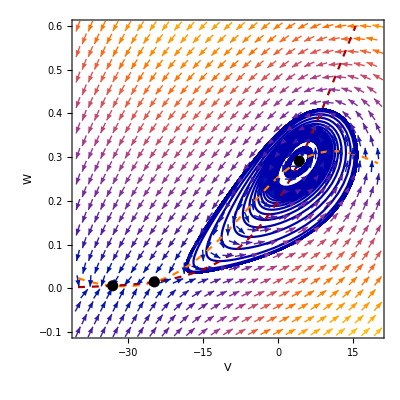

```mathematica
phasePortrait[9.2,{{4.25, 0.31},{4.25, 0.33}}]
```

What does this suggest about the area between the stable equilibrium point and the stable limit cycle?

Q9: It can be shown that the Hopf bifurcation is sub-critical. How does this piece of information fit in with your answer to the previous question?

The subcritical variant of the Hopf bifurcation is associated with the emergence of an unstable limit cycle that branches off from the equilibrium point at the bifurcation point. This fits with our earlier conclusion. Apparently, at Ca ≈9.265, ...

### Following the fate of the limit cycle

Given that the stable limit cycle does not originate at the Hopf bifurcation point, we will now try to find out what happens to the cycle as the intracellular Ca^(2+)concentration is varied. One way to do this is to run a simulation until it converges on the cycle and then record the lowest and the highest value of the membrane potential observed along the limit cycle. By repeating this procedure for a range of different Ca^(2+)concentrations, we can get a quick impression of how the amplitude of the oscillations changes with the value of the parameter. Below is a procedure that produces the desired data

```mathematica
followLimitCycle[Ca0_,Ca1_, initialCondition_List] := Module[
{nStep = 40,Ca,sys, vars, tConverge,tCycle, init, solution,pts},
tConverge = 1000.0;
tCycle = 1000.0;
vars = {V[t], W[t]};
init = Thread[{V[0], W[0]} == initialCondition] ;

  (* do for a range of calcium concentrations *)
  pts=Reap[Do[
Ca=Ca0+i(Ca1-Ca0)/nStep;
sys={D[V[t],t]==eqV[V[t],W[t],Ca],D[W[t],t]==eqW[V[t],W[t]]}/.pars;

(* allow to converge on cycle *)
solution=NDSolve[Join[sys,init],vars,{t,0,tConverge}];

(* simulate dynamics along cycle *)
init = Thread[{V[0], W[0]} == {V[t],W[t]}]/.solution/.{t->tConverge} ;
solution=NDSolve[Join[sys,init],vars,{t,0,tCycle}];

(* locate minimum and maximum value *)
Sow[{Ca,NMinValue[{V[t]/.solution//First,0≤ t≤ tCycle},t]},minval];
Sow[{Ca,NMaxValue[{V[t]/.solution//First,0≤ t≤ tCycle},t]},maxval];

(* use last point as initial point for next simulation*)
init =  Thread[{V[0], W[0]} == {V[t],W[t]}]/.solution/.{t->tCycle} 
   ,{i,0,nStep}]][[2]]
]
```

The figure below indicates the range of the membrane potential (minimum & maximum) as it oscillates along the stable limit cycle. The points are shown for Ca^(2+)concentrations between 2 and 9.5, and superimposed on the curves that indicate the location of the equilibrium points. The red dot pinpoints the position of the Hopf bifurcation point.

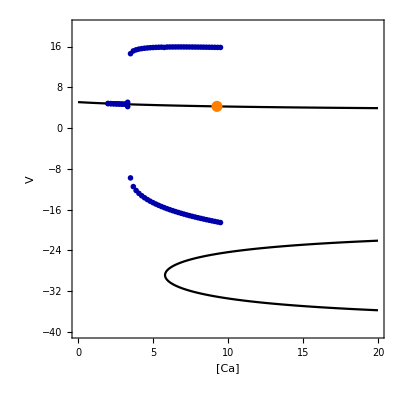

```mathematica
plLeft=Show[equilibria,ListPlot[followLimitCycle[9.5,2.0,{4.0,0.25}], PlotStyle -> {{Darker[Blue], PointSize[0.01]}}],Graphics[{Orange,PointSize[0.02],Point[{9.265,4.250844678619417}]}]]
```

Q10: The amplitude of the stable limit cycle at first decreases gradually with the calcium concentration, but there appears to be a sudden change at Ca ≈ 3.5. Examine how the phaseportrait changes around this point, and infer what kind of bifurcation occurs, making use of the insights you obtained in the previous two questions.

We first look to the right of the sudden change, at Ca = 3.6

Trajectory 1 : initial point {V[0]==-8.47,W[0]==0.208}, final point {{V[1000.]==7.80202,W[1000.]==0.40556}}

Trajectory 2 : initial point {V[0]==-6.,W[0]==0.208}, final point {{V[1000.]==4.66666,W[1000.]==0.299387}}

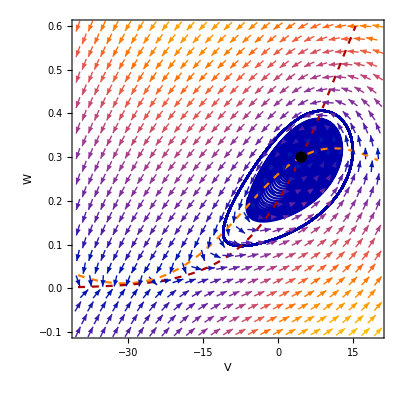

```mathematica
phasePortrait[3.6,{{-8.47, 0.208},{-6.0, 0.208}}]
```

We then look to the lft of the sudden change, at Ca = 3.4

Trajectory 1 : initial point {V[0]==-8.8,W[0]==0.208}, final point {{V[1000.]==-0.423994,W[1000.]==0.155226}}

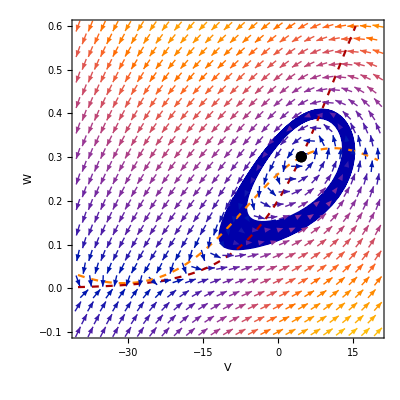

```mathematica
phasePortrait[3.4,{{-8.8, 0.208}}]
```

What limit cycles are seen in each? What has changed between the two phaseportraits?

Q11: Return to the bifurcation diagram you sketched in Q6, and add lines to indicate the amplitude of the stable limit cycle. Do the same for the unstable limit cycle that emerges from the Hopf bifurcation point and show how these connect to the maximum and minimum of the stable limit cycle. A qualitative picture is good enough; it is very difficult to locate the exact position of the unstable cycle by simulation.

To complete our analysis, we also follow the stable limit cycle as we gradually increase the Ca^(2+)concentration. The data are added to the previous figure

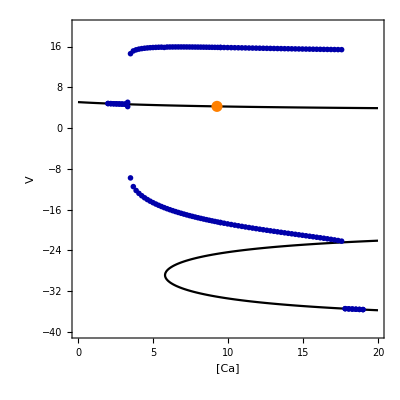

```mathematica
plFull=Show[plLeft,ListPlot[followLimitCycle[9.5,19.0,{4.0,0.25}], PlotStyle -> {{Darker[Blue], PointSize[0.01]}}]]
```

Also at a high  Ca^(2+)concentration the stable limit cycle appears to collapse suddenly. Below is a phase-portrait showing the stable limit cycle at Ca=17.8, just before it disappears.

```mathematica
phasePortrait[17.8,{{-22.109208183373173,0.023591190228318504}}]
```

Q12: What kind of bifurcation is responsible for the loss of the cycle at high Ca^(2+)concentrations?

The stable limit cycle connects to the saddle point, establishing a...
Afterwards, the cycles has disappeared.

Q13: Imagine that you would be able to experimentally manipulate the intracellular Ca^(2+)concentration in a pancreatic β-cell. How would the electrical activity of the cell change if you would very slowly increase the Ca^(2+)concentration from 0 to 20? How would it change if you would next decrease the concentration to 0 again?

Starting from low Ca^(2+) concentrations, the system would initially stabilise at the stable spiral point (i.e., at high V) and stay there until the stability of the equilibrium is lost at the... (around [Ca^(2+)] = 9.2).
After that, the system would jump to the closest stable attractor, which is the...
The amplitude of the ... would increase as [Ca^(2+) ] increases, up to the point that it connects to the... (shortly after [Ca^(2+)] = ...).
The system will then converge on the only remaining stable attractor, the equilibrium at low V, which corresponds to the ...

If the Ca^(2+) is decreased again from that point onwards, the cell would stay trapped in the resting state equilibrium, until this equilibrium disappears through a ... (around [Ca^(2+)] = ...). From there, the system would be forced to converge to the ..., and it would remain on that attractor until ... at [Ca^(2+)] = ... . At even lower [Ca^(2+)], the cell would converge on the only remaining equilibrium, ... .

### Modelling the bursting behaviour

Now that we understand how  Ca^(2+)controls the transition between the oscillatory and resting phase, we are ready to model the spontaneous bursting observed in pancreatic β-cells. For this purpose, we extend the model with an additional equation that describes the change of the intracellular  Ca^(2+)concentration.

```mathematica
eqCa[V_,Ca_]:=0.002(-0.2 Subscript[g, ca] Subscript[m, ∞][V](V-Subscript[v, ca])-Ca)
```

A simulation of the extended model nicely shows the bursting behaviour, triggered by a slow decrease of Ca^(2+)during the resting phase and an increase of Ca^(2+)during the oscillatory phase.

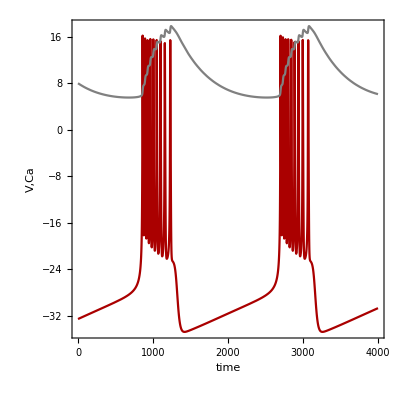

```mathematica
tEnd = 4000.0;
sys={D[V[t],t]==eqV[V[t],W[t],Ca[t]],D[W[t],t]==eqW[V[t],W[t]],D[Ca[t],t]==eqCa[V[t],Ca[t]]}/.pars;
vars={V[t],W[t],Ca[t]};
init={V[0]==-32.53787782518964,W[0]==0.00593584822774111,Ca[0]==7.995453830994973};
solution=NDSolve[Join[sys,init],vars,{t,0,tEnd}];
Plot[Evaluate[{V[t],Ca[t]}/.solution],{t,0,tEnd},PlotStyle->{Darker[Red],Gray},Frame->True,FrameLabel->{"time","V,Ca"},AspectRatio->1]
```

When the trajectory is superimposed on the bifurcation diagram (shown below with orange dots indicating the different bifurcation points), it becomes clear that the slow change of the Ca^(2+) concentration pushes the system through the homoclinic and the fold bifurcation, inducing a repetitive switch from the stable fixed point to the periodic attractor and back.

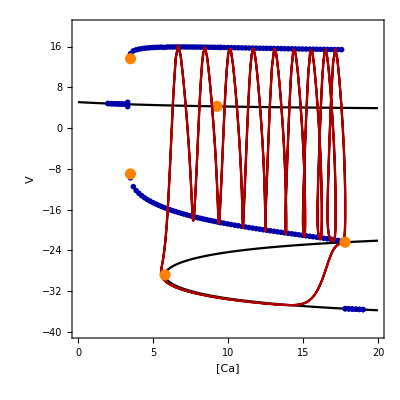

```mathematica
Show[
plFull,
ParametricPlot[{Ca[t], V[t]} /. solution, {t, 0, tEnd}, PlotStyle-> Darker[Red],PlotRange ->{{0, 20}, {-40, 20}}, Frame -> True , AspectRatio -> 1],
Graphics[{Orange,PointSize[0.02],
Point[{5.802,-28.83}],
Point[{17.8,-22.41}],
Point[{3.5,-9.0}],
Point[{3.5,13.6}]}]
]
```

Q14: A characteristic feature of the bursting of pancreatic β-cells is that the interval between spikes grows as the cell comes closer to the end of the bursting period. Do you also observe this feature in the model? Can you give a mathematical explanation for why the slowing down occurs?

Yes, the slowing down is clearly visible in the time series plots. It is caused by the fact that the dynamics along the limit cycle becomes very slow when the cycle gets closer to...

Q15: Bursting can be generated by different mechanisms. Which other mechanism is suggested by the bifurcation diagram of the pancreatic β-cell? Will this type of bursting also show a slowing down of the electrical spiking toward the end of the oscillatory phase?